Your Title Here

```mathematica
Module[{data},
data[list_]:=SortBy[DeleteDuplicates@Join[(list[[#]]+list[[#+1]])/2&/@Range[1,Length@list-1,2],list],First];
Show[diagram,ListPlot[data[P2],Joined->True,PlotStyle->{Thick,Dashed,Black}],PlotLabel->Length@data[P2]];
data[P2]
]
```

{{200.,0.062},{205.,0.082},{210.,0.102},{220.,0.142},{225.,0.172},{230.,0.202},{240.,0.262},{245.,0.312},{250.,0.362},{260.,0.462},{265.,0.512},{270.,0.562},{280.,0.702},{285.,0.772},{290.,0.842},{300.,1.016},{305.,1.096},{310.,1.176},{320.,1.376},{325.,1.476},{330.,1.576},{340.,1.776},{345.,1.876},{350.,1.976},{360.,2.196},{365.,2.306},{370.,2.416},{380.,2.656},{385.,2.766},{390.,2.876},{400.,3.096},{405.,3.206},{410.,3.316},{420.,3.536},{425.,3.646},{430.,3.756},{440.,3.976},{445.,4.075},{450.,4.174},{460.,4.374},{465.,4.4665},{470.,4.559},{480.,4.72},{485.,4.775},{490.,4.83},{500.,4.87},{503.015,4.85445},{506.03,4.83889},{510.,4.78},{511.582,4.74},{513.163,4.7}}

```mathematica
Length@P3
```

32

```mathematica
Module[{pt},
pt={{485.6,1.4},{489.8,1.5}};
{(pt[[1,1]]+pt[[2,1]])/2,(pt[[1,2]]+pt[[2,2]])/2}]
```

{487.7,1.45}

```mathematica
P1={{200.,0.021},{215.,0.041},{230.,0.061},{245.,0.101},{260.,0.141},{275.,0.201},{290.,0.281},{305.,0.357},{320.,0.437},{335.,0.537},{350.,0.657},{365.,0.777},{380.,0.917},{395.,1.057},{410.,1.219},{425.,1.419},{440.,1.619},{455.,1.839},{470.,2.099},{485.,2.379},{500.,2.695},{515.,3.035},{521.8345228898426,3.2},{525.7339055793991,3.2675017660714687},{530.,3.3},{532.68,3.29}};
```

```mathematica
T1={{367.5,0.1},{379.9,0.15000000000000002},{392.3,0.2},{408.7,0.3},{421.1,0.4},{431.3,0.5},{440.16,0.6},{443.96000000000004,0.6499999999999999},{447.76,0.7},{451.26,0.75},{454.76,0.8},{460.96,0.9},{466.56,1.},{472.,1.1},{476.8,1.2},{481.4,1.3},{483.5,1.35},{485.6,1.4},{487.70000000000005,1.45},{489.8,1.5},{493.56,1.6},{497.16,1.7},{500.56,1.8},{503.96,1.9},{506.96,2.},{509.93,2.1},{512.93,2.2},{515.53,2.3},{518.13,2.4},{520.53,2.5},{523.01,2.6},{525.21,2.7},{527.21,2.8},{529.11,2.9},{530.81,3.},{532.32,3.1},{533.5,3.197570030947016},{533.7,3.2507078978234234},{532.68,3.29}};
```

```mathematica
P2={{200.,0.062},{210.,0.102},{220.,0.142},{230.,0.202},{240.,0.262},{250.,0.362},{260.,0.462},{270.,0.562},{280.,0.702},{290.,0.842},{300.,1.016},{310.,1.176},{320.,1.376},{330.,1.576},{340.,1.776},{350.,1.976},{360.,2.196},{370.,2.416},{380.,2.656},{390.,2.876},{400.,3.096},{410.,3.316},{420.,3.536},{430.,3.756},{440.,3.976},{450.,4.174},{460.,4.374},{470.,4.559},{480.,4.72},{490.,4.83},{500.,4.87},{506.0300429184549,4.838891036313316},{510.,4.78},{513.163,4.7}};
```

```mathematica
T2={{359.1,0.1},{382.5,0.2},{397.7,0.3},{409.3,0.4},{418.7,0.5},{426.82,0.6},{433.82,0.7},{440.02,0.8},{445.62,0.9},{450.62,1.},{455.36,1.1},(*{459.76,1.2},*){463.76,1.3},{467.56,1.4},{471.16,1.5},{474.5,1.6},{477.5,1.7},{480.5,1.8},{483.3,1.9},{486.1,2.},{488.48,2.1},{490.88,2.2},{493.28,2.3},{495.48,2.4},{497.48,2.5},{499.52,2.6},{501.32,2.7},{503.12,2.8},{504.72,2.9},{506.32,3.},{507.8,3.1},(*{509.2,3.2},*){510.5,3.3},{511.7,3.4},{512.82,3.5},{513.93,3.6},{514.77,3.7},{515.53,3.8},{516.33,3.9},{516.93,4.},{517.32,4.1},{517.52,4.2},{517.52,4.3},{517.52,4.4},{517.08,4.5},{515.29,4.6},{513.16,4.7}};
```

```mathematica
P3={{200.,0.104},{210.,0.164},{220.,0.244},{230.,0.344},{240.,0.464},{250.,0.604},{260.,0.784},{270.,0.984},{280.,1.224},{290.,1.484},{300.,1.774},{310.,2.094},{320.,2.434},{330.,2.794},{340.,3.154},{350.,3.534},{360.,3.914},{370.,4.294},{380.,4.674},{390.,5.034},{400.,5.374},{410.,5.694},{420.,5.994},{430.,6.274},{440.,6.494},{450.,6.669},{460.,6.779},{470.,6.826},{480.,6.78},{486.,6.6443337923465595},{490.,6.451},{490.5,6.4}};
```

```mathematica
T3={{348.84,0.1},{384.24,0.3},{403.44,0.5},{417.04,0.7},{427.64,0.9},{436.31,1.1},{443.71,1.3},{450.31,1.5},{455.91,1.7},{460.91,1.9},{465.46,2.1},{469.46,2.3},{473.06,2.5},{476.46,2.7},{479.46,2.9},{482.11,3.1},{484.51,3.3},{486.71,3.5},{488.7,3.7},{490.51,3.9},{492.01,4.1},{493.19,4.3},{494.21,4.5},{495.01,4.7},{495.62,4.9},{495.95,5.1},{496.06,5.3},{495.71,5.5},{495.26,5.7},{494.44,5.9},{493.48,6.1},{491.57,6.3},{490.5,6.4}};
```

```mathematica
P4={{200.,0.145},{210.,0.225},{220.,0.345},{230.,0.485},{240.,0.645},{250.,0.865},{260.,1.125},{270.,1.445},{280.,1.805},{290.,2.205},{300.,2.653},{310.,3.153},{320.,3.673},{330.,4.233},{340.,4.793},{350.,5.378},{360.,5.938},{370.,6.478},{380.,6.978},{390.,7.438},{400.,7.824},{410.,8.141},{420.,8.351},{430.,8.451},{435.197,8.479},{440.,8.44},{444.41,8.3567},{448.078,8.2}};
```

```mathematica
T4={{334.42,0.1},{375.42,0.4},{394.82,0.7},{408.02,1.},{417.82,1.3},{423.39,1.5},{430.39,1.8},{436.19,2.1},{441.19,2.4},{445.39,2.7},{447.840,2.9},{451.14,3.2},{453.98,3.5},{456.400,3.80},{458.46,4.1},{459.66,4.3},{461.06,4.6},{462.26,4.9},{463.06,5.2},{463.56,5.5},{463.85,5.8},{463.8,6.},{463.44,6.3},{462.71,6.6},{461.5,6.9},{459.780,7.2},{457.38,7.5},{455.25,7.7},{451.5,8.},{448.08,8.2}};
```

```mathematica
P5={{200.,0.166},{210.,0.266},{220.,0.386},{230.,0.546},{240.,0.746},{250.,1.005},{260.,1.325},{270.,1.685},{280.,2.105},{290.,2.585},{300.,3.142},{310.,3.742},{320.,4.382},{330.,5.042},{340.,5.722},{350.,6.394},{360.,7.034},{370.,7.607},{380.,8.094},{390.,8.474},{394.9570815450645,8.61667177605582},{400.,8.713},{404.82832618025765,8.750003332210317},{411.,8.75}};
```

```mathematica
T5={{323.79,0.1},{350.66,0.288},{374.39,0.6},{394.39,1.1},{406.99,1.6},{416.07,2.1},{422.87,2.6},{428.27,3.1},{432.27,3.6},{435.27,4.1},{437.47,4.6},{439.07,5.1},{439.67,5.6},{439.77,6.1},{438.97,6.6},{437.27,7.1},{434.37,7.6},{431.7,8.},{428.65,8.28},{421.,8.63},{416.,8.72},{411.,8.75}};
```

```mathematica
P6={{200.,0.187},{205.,0.247},{210.,0.307},{215.,0.367},{220.,0.447},{225.,0.527},{230.,0.627},{235.,0.727},{240.,0.867},{245.,0.987},{250.,1.147},{255.,1.327},{260.,1.507},{265.,1.707},{270.,1.927},{275.,2.167},{280.,2.427},{285.,2.707},{290.,3.007},{295.,3.327},{300.,3.651},{305.,4.011},{310.,4.371},{315.,4.751},{320.,5.131},{325.,5.531},{330.,5.911},{335.,6.292},{340.,6.662},{345.,7.012},{350.,7.332},{355.,7.632},{360.,7.872},{365.,8.052},{370.,8.204},{375.,8.278},{375.,8.278}};
```

```mathematica
T6={{323.37,0.2},{340.77,0.4},{351.57,0.6},{359.57,0.8},{365.97,1.},{370.97,1.2},{375.37,1.400},{379.17,1.6},{382.37,1.8},{385.17,2.},{387.58,2.2},{389.98,2.4},{391.78,2.6},{393.58,2.800},{395.18,3.},{396.58,3.2},{397.78,3.4},{398.98,3.6},{399.78,3.800},{400.58,4.},{401.37,4.2},{401.95,4.4},{402.41,4.600},{402.77,4.8},{403.03,5.},{403.17,5.2},{403.21,5.4},{403.15,5.600},{402.97,5.8},{402.68,6.},{402.24,6.2},{401.72,6.4},{401.04,6.600},{400.2,6.8},{399.2,7.},{397.96,7.2},{396.49,7.4},{394.68,7.600},{392.38,7.8},{389.28,8.},{384.18,8.2},{383.33,8.22},{382.65,8.24},{380.65,8.26},{375.,8.28}};
```

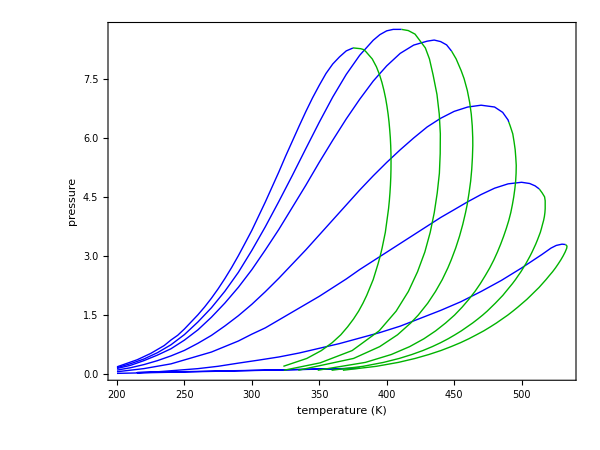

```mathematica
diagram=Show[ListPlot[#,Joined->True,PlotStyle->{{Thick,Blue},{Thick,RGBColor[0,0.7,0]}}]&/@{{P1,T1},{P2,T2},{P3,T3},{P4,T4},{P5,T5},{P6,T6}},
PlotRange->All,Frame->True,FrameLabel->{"temperature (K)","pressure"},LabelStyle->{17,Black},ImageSize->{600,450},AspectRatio->Full]
```

```mathematica
Length@#&/@{T1,T2,T3,T4,T5,T6}
```

{39,45,33,30,22,45}

```mathematica
47-34
```

13





```mathematica
Manipulate[
Module[{P,T,rP,rT,newP,newT},
P={{200,0.18688916963079638},{201,0.2068891696307964},{202,0.2068891696307964},{203,0.22688916963079642},{204,0.22688916963079642},{205,0.24688916963079643},{206,0.24688916963079643},{207,0.26688916963079645},{208,0.26688916963079645},{209,0.28688916963079647},{210,0.3068891696307965},{211,0.3068891696307965},{212,0.3268891696307965},{213,0.3268891696307965},{214,0.3468891696307965},{215,0.36688916963079654},{216,0.38688916963079656},{217,0.38688916963079656},{218,0.4068891696307966},{219,0.4268891696307966},{220,0.4468891696307966},{221,0.4468891696307966},{222,0.46688916963079663},{223,0.48688916963079665},{224,0.5068891696307967},{225,0.5268891696307967},{226,0.5468891696307967},{227,0.5668891696307967},{228,0.5868891696307967},{229,0.6068891696307968},{230,0.6268891696307968},{231,0.6468891696307968},{232,0.6668891696307968},{233,0.6868891696307968},{234,0.7068891696307968},{235,0.7268891696307969},{236,0.7668891696307969},{237,0.7868891696307969},{238,0.8068891696307969},{239,0.826889169630797},{240,0.866889169630797},{241,0.886889169630797},{242,0.906889169630797},{243,0.9468891696307971},{244,0.9668891696307971},{245,0.9868891696307971},{246,1.0268891696307971},{247,1.0468891696307971},{248,1.0868891696307972},{249,1.1268891696307972},{250,1.1468891696307972},{251,1.1868891696307973},{252,1.2068891696307973},{253,1.2468891696307973},{254,1.2868891696307974},{255,1.3268891696307974},{256,1.3468891696307974},{257,1.3868891696307974},{258,1.4268891696307975},{259,1.4668891696307975},{260,1.5068891696307976},{261,1.5468891696307976},{262,1.5868891696307976},{263,1.6268891696307977},{264,1.6668891696307977},{265,1.7068891696307977},{266,1.7468891696307978},{267,1.7868891696307978},{268,1.8468891696307979},{269,1.886889169630798},{270,1.926889169630798},{271,1.986889169630798},{272,2.0268891696307976},{273,2.0668891696307967},{274,2.1268891696307954},{275,2.1668891696307946},{276,2.2268891696307933},{277,2.2668891696307925},{278,2.326889169630791},{279,2.38688916963079},{280,2.426889169630789},{281,2.4868891696307878},{282,2.5468891696307865},{283,2.5868891696307856},{284,2.6468891696307844},{285,2.706889169630783},{286,2.766889169630782},{287,2.8268891696307805},{288,2.8868891696307792},{289,2.946889169630778},{290,3.0068891696307767},{291,3.0668891696307754},{292,3.126889169630774},{293,3.186889169630773},{294,3.266889169630771},{295,3.32688916963077},{296,3.3868891696307686},{297,3.4468891696307673},{298,3.5268891696307656},{299,3.5868891696307643},{300,3.651346736207476},{301,3.7313467362074744},{302,3.791346736207473},{303,3.8713467362074714},{304,3.93134673620747},{305,4.011346736207469},{306,4.071346736207468},{307,4.151346736207466},{308,4.231346736207464},{309,4.291346736207463},{310,4.371346736207461},{311,4.4513467362074595},{312,4.531346736207458},{313,4.5913467362074565},{314,4.671346736207455},{315,4.751346736207453},{316,4.831346736207451},{317,4.91134673620745},{318,4.991346736207448},{319,5.051346736207447},{320,5.131346736207445},{321,5.211346736207443},{322,5.291346736207442},{323,5.37134673620744},{324,5.451346736207438},{325,5.531346736207436},{326,5.611346736207435},{327,5.691346736207433},{328,5.771346736207431},{329,5.83134673620743},{330,5.911346736207428},{331,5.991346736207427},{332,6.071346736207425},{333,6.151743831767006},{334,6.221743831767005},{335,6.291743831767003},{336,6.371743831767001},{337,6.444243831767},
{338,6.516743831766998},{339,6.589243831766996},{340,6.661743831766995},{341,6.734243831766994},{342,6.806743831766992},{343,6.87924383176699},{344,6.951743831766989},{345,7.011743831766988},{346,7.091743831766986},{347,7.151743831766985},{348,7.2117438317669835},{349,7.271743831766982},{350,7.331743831766981},{351,7.39174383176698},{352,7.451743831766978},{353,7.511743831766977},{354,7.571743831766976},{355,7.631743831766975},{356,7.671743831766974},{357,7.731743831766972},{358,7.771743831766972},{359,7.83174383176697},{360,7.8717438317669695},{361,7.911743831766969},{362,7.951743831766968},{363,7.991743831766967},{364,8.031743831766967},{365,8.051743831766967},{366,8.096987195157915},{367,8.127427195156763},{368,8.155467195155701},{369,8.181047195154733},{370,8.20410719515386},{370,8.204102457787064},{371,8.224528893530037},{373,8.257182193671607},{374,8.267842193671203},{375,8.278309330737184}};

T={{323.3663343376186,0.2},{333.36633433762086,0.30000},{340.76633433762254,0.4},{346.7663343376239,0.5},{351.566334337625,0.6},{355.966334337626,0.7},{359.5663343376268,0.7999999999999999},{362.9663343376276,0.8999999999999999},{365.96633433762827,0.9999999999999999},{368.56633433762886,1.0999999999999999},{370.9663343376294,1.2},{373.36633433762995,1.3},{375.3663343376304,1.400},{377.36633433763086,1.500},{379.16633433763127,1.600},{380.76633433763163,1.7000},{382.366334337632,1.800},{383.7663343376323,1.9000000000000006},{385.16633433763263,2.0000},{386.3663343376329,2.100},{387.57610797844086,2.2},{388.77610797844113,2.300},{389.9761079784414,2.4000},{390.97610797844163,2.5000},{391.7761079784418,2.600},{392.77610797844204,2.7000000000000006},{393.5761079784422,2.8000000000000007},{394.3761079784424,2.90},{395.1761079784426,3.00},{395.97610797844277,3.10},{396.5761079784429,3.20},{397.17610797844304,3.30},{397.7761079784432,3.402},{398.3761079784433,3.503},{398.97610797844345,3.604},{399.37610797844354,3.705},{399.77610797844363,3.806},{400.37610797844377,3.907},{400.5761079784438,4.00},{400.9761079784439,4.10},{401.369,4.199999999999999},{401.6728299427992,4.299999999999999},{401.9528299427989,4.399999999999999},{402.1928299427987,4.499999999999998},{402.4128299427985,4.599999999999998},{402.6128299427983,4.6999999999999975},{402.7728299427982,4.799999999999997},{402.91282994279806,4.899999999999997},{403.03282994279795,4.9999999999999964},{403.1128299427979,5.099999999999996},{403.1728299427978,5.199999999999996},{403.2128299427978,5.299999999999995},{403.2128299427978,5.399999999999995},{403.20182994283463,5.499999999999995},{403.15282994279784,5.599999999999994},{403.0728299427979,5.699999999999994},{402.972829942798,5.799999999999994},{402.83585536192817,5.899999999999993},{402.67963432974415,5.999999999999993},{402.48015105828256,6.0999999999999925},{402.2401510582828,6.199999999999999},{402.000151058283,6.299999999999999},{401.72015105828325,6.399999999999999},{401.39996496548594,6.499999999999998},{401.04015105828387,6.599999999999998},{400.64015105828423,6.6999999999999975},{400.20015105828463,6.799999999999997},{399.72015105828507,6.899999999999997},{399.20015105828554,6.9999999999999964},{398.6001510582861,7.099999999999996},{397.96015105828667,7.199999999999996},{397.264550710906,7.299999999999995},{396.49001163035337,7.399999999999995},{395.6401510582888,7.499999999999995},{394.68015105828965,7.599999999999994},{393.60015105829063,7.699999999999994},{392.38015105829174,7.799999999999994},{390.96015105829304,7.899999999999993},{389.28015105829456,7.999999999999993},{387.1776021520329,8.1},{384.1776021520329,8.2},{383.6703423269868,8.21},{383.33034232698694,8.22},{382.99034232698707,8.23},{382.6503423269872,8.24},{381.8103423269873,8.25},{380.65034232698747,8.26},{378.5103423269876,8.27},{375,8.278309330737184}};
(****************************)

newP=Round[Join[P[[#]]&/@Range[1,Length@P,5],{Last@T}],0.001];
newT=Round[T[[#]]&/@Range[1,Length@T,2],0.01];

ListPlot[{newP,newT},Joined->True,PlotStyle->{{Thick,Blue},{Thick,RGBColor[0,0.7,0]}},(*PlotRange->{{325,450},{7,9}},*)Frame->True,ImageSize->600,PlotLabel->{Length@newP,Length@newT},Epilog->If[bmth,{PointSize@0.01,Blue,Point@newP,RGBColor[0,0.7,0],Point@newT},{}]];newT
],
Control[{{bmth,False},{True,False}}],
SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX